```mathematica
Integrate[ 1,{j,0,x}]
Integrate[ 1,{j,0,x}, {k,0,j}]
Integrate[ 1,{j,0,x}, {k,0,j}, {l,0,k}]
Integrate[ 1,{j,0,x}, {k,0,j}, {l,0,k}, {m,0,l}]
```

x

x^2/2

x^3/6

x^4/24

```mathematica
Integrate[ 1,{j,1,x}]
Integrate[ 1,{j,1,x}, {k,1,j}]
Integrate[ 1,{j,1,x}, {k,1,j}, {l,1,k}]
Integrate[ 1,{j,1,x}, {k,1,j}, {l,1,k}, {m,1,l}]
```

-1+x

1/2-x+x^2/2

1/6 (-1+x)^3

1/24 (-1+x)^4

```mathematica
Integrate[ 1/j,{j,1,x}]
Integrate[ 1/(j k),{j,1,x}, {k,1,x/j}]
Integrate[ 1/(j k l),{j,1,x}, {k,1,x/j}, {l,1,x/(j k)}]
Integrate[ 1/(j k l m),{j,1,x}, {k,1,x/j}, {l,1,x/(j k)}, {m,1,x/(j k l)}]
```

ConditionalExpression[Log[x],Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^2/2,Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^3/6,Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^4/24,Re[x]≥0||x∉Reals]

```mathematica
Expand[Integrate[ 1,{j,1,x}]]
Expand[Integrate[ 1,{j,1,x}, {k,1,x/j}]]
Expand[Integrate[ 1,{j,1,x}, {k,1,x/j}, {l,1,x/(j k)}]]
Expand[Integrate[ 1,{j,1,x}, {k,1,x/j}, {l,1,x/(j k)}, {m,1,x/(j k l)}]]
```

-1+x

ConditionalExpression[1-x+x Log[x],Re[x]≥0||x∉Reals]

ConditionalExpression[-1+x-x Log[x]+1/2 x Log[x]^2,Re[x]≥0||x∉Reals]

ConditionalExpression[1-x+x Log[x]-1/2 x Log[x]^2+1/6 x Log[x]^3,Re[x]≥0||x∉Reals]

```mathematica
Integrate[ 1/j,{j,1,x}]
Integrate[ 1/(j k),{j,1,x}, {k,1,j}]
Integrate[ 1/(j k l),{j,1,x}, {k,1,j}, {l,1,k}]
Integrate[ 1/(j k l m),{j,1,x}, {k,1,j}, {l,1,k}, {m,1,l}]
```

ConditionalExpression[Log[x],Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^2/2,Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^3/6,Re[x]≥0||x∉Reals]

ConditionalExpression[Log[x]^4/24,Re[x]≥0||x∉Reals]

```mathematica
Sum[ 1/j,{j,1,x}]
Sum[ 1/(j k),{j,1,x}, {k,1,j}]
Sum[ 1/(j k l),{j,1,x}, {k,1,j}, {l,1,k}]
Sum[ 1/(j k l m),{j,1,x}, {k,1,j}, {l,1,k}, {m,1,l}]
```

HarmonicNumber[x]

1/6 (π^2+3 HarmonicNumber[x]^2-3 HarmonicNumber[x,2]-6 PolyGamma[1,1+x])

∑_(j=1)^x ∑_(k=1)^j ∑_(l=1)^k 1/(j k l)

∑_(j=1)^x ∑_(k=1)^j ∑_(l=1)^k ∑_(m=1)^l 1/(j k l m)

```mathematica
Sum[ 1,{j,2,x}]
Sum[ 1,{j,2,x}, {k,2,j}]
Sum[ 1,{j,2,x}, {k,2,j}, {l,2,k}]
Sum[ 1,{j,2,x}, {k,2,j}, {l,2,k}, {m,2,l}]
```

-1+x

1/2 (-1+x) x

1/6 (-1+x) x (1+x)

1/24 (-1+x) x (1+x) (2+x)

```mathematica
Sum[ 1,{j,1,x}]
Sum[ 1,{j,1,x}, {k,1,j}]
Sum[ 1,{j,1,x}, {k,1,j}, {l,1,k}]
Sum[ 1,{j,1,x}, {k,1,j}, {l,1,k}, {m,1,l}]
```

x

1/2 x (1+x)

1/6 x (1+x) (2+x)

1/24 x (1+x) (2+x) (3+x)

```mathematica
Expand[1/6 x (1+x) (2+x)]
```

x/3+x^2/2+x^3/6

```mathematica
Sum[j^(-1),{j,1,n}]
```

HarmonicNumber[n]

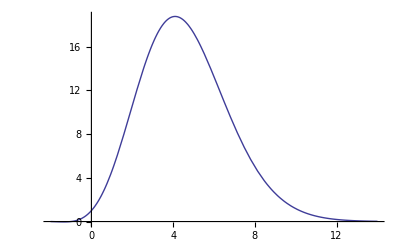

```mathematica
Plot[ Log[100]^k/Gamma[k+1],{k,-2,14}]
```

```mathematica
FullSimplify[Log[n]^k/Gamma[k+1]]
```

Log[n]^k/Gamma[1+k]

```mathematica
FullSimplify[(n-1)^k/Gamma[k+1]]
```

(-1+n)^k/Gamma[1+k]

```mathematica
FullSimplify[(n)^k/Gamma[k+1]]
```

n^k/Gamma[1+k]